```mathematica
ClearAll;
```

```mathematica
(*Funções Auxiliares *)
Zeros[i_,j_]:= ConstantArray[0,{i,j}];
Eye[n_]:= IdentityMatrix[n];

NRow[M_]:= Dimensions[M]⟦1⟧;
NCol[M_]:= Dimensions[M]⟦2⟧;
NVec[v_]:= Dimensions[v]⟦1⟧;

Inv[M_]:= Inverse[M];

Diag[M1_,M2_] := Join[ Join[M1,Zeros[NRow@M2,NCol@M1]],Join[Zeros[NRow@M1,NCol@M2],M2]  ,2];
Diag[M1_,M2_,M3_] := Diag[Diag[M1,M2],M3];
Diag[M1_,M2_,M3_,M4_] := Diag[Diag[M1,M2,M3],M4];
```

```mathematica
𝓇 = "RR";
```

```mathematica
Subscript[ν#, 𝓇]=2;
```

```mathematica
Subscript[NΩ, #]={1,2};
Subscript[NΩ, o]=Complement[Range[Subscript[ν#, 𝓇]],Subscript[NΩ, #]];
Subscript[NV, #]={};
Subscript[NV, o]=Complement[Range[2 Subscript[ν#, 𝓇]],Subscript[NV, #]];
```

```mathematica
Subscript[𝕢#, 𝓇]={Subscript[θ, 𝓇,1][t],Subscript[θ, 𝓇,2][t]};
Subscript[𝕢.ba, 𝓇]={Subscript[x, 𝓇,1][t],Subscript[y, 𝓇,1][t],Subscript[x, 𝓇,2][t],Subscript[y, 𝓇,2][t]};
Subscript[𝕢, 𝓇]=Join[Subscript[𝕢#, 𝓇],Subscript[𝕢.ba, 𝓇]];
Subscript[ν.ba, q,𝓇]=NVec@Subscript[𝕢.ba, 𝓇];
```

```mathematica
Subscript[𝕨, ω,𝓇] ={Subscript[ω, 𝓇,z1][t],Subscript[ω, 𝓇,z2][t]};
Subscript[𝕨, v,𝓇] = {Subscript[v, 𝓇,x1][t],Subscript[v, 𝓇,y1][t],Subscript[v, 𝓇,x2][t],Subscript[v, 𝓇,y2][t]};
Subscript[𝕡#, 𝓇]=Join[Subscript[𝕨, ω,𝓇]⟦Subscript[NΩ, #]⟧,Subscript[𝕨, v,𝓇]⟦Subscript[NV, #]⟧];
Subscript[𝕡.ba, 𝓇]=Join[Subscript[𝕨, ω,𝓇]⟦Subscript[NΩ, o]⟧,Subscript[𝕨, v,𝓇]⟦Subscript[NV, o]⟧];
Subscript[𝕡, 𝓇]=Join[Subscript[𝕡#, 𝓇],Subscript[𝕡.ba, 𝓇]];
Subscript[ν.ba, p,𝓇]=NVec@Subscript[𝕡.ba, 𝓇];
```

```mathematica
s2Sin = {
Subscript[c, 1]->Cos[Subscript[θ, 𝓇,1][t]],
Subscript[s, 1]->Sin[Subscript[θ, 𝓇,1][t]],
Subscript[c, 2]->Cos[Subscript[θ, 𝓇,2][t]],
Subscript[s, 2]->Sin[Subscript[θ, 𝓇,2][t]] };
```

```mathematica
Sin2s = {
Cos[Subscript[θ, 𝓇,1][t]]-> Subscript[c, 1],
Sin[Subscript[θ, 𝓇,1][t]]-> Subscript[s, 1],
Cos[Subscript[θ, 𝓇,2][t]]-> Subscript[c, 2],
Sin[Subscript[θ, 𝓇,2][t]]-> Subscript[s, 2],
Cos[Subscript[θ, 𝓇,1][t]+Subscript[θ, 𝓇,2][t]]-> Subscript[c, 12],
Sin[Subscript[θ, 𝓇,1][t]+Subscript[θ, 𝓇,2][t]]-> Subscript[s, 12]};
```

```mathematica
Subscript[ℤ, 1]={{Subscript[c, 1],-Subscript[s, 1],0},{Subscript[s, 1],Subscript[c, 1],0},{0,0,1}}/.s2Sin;
Subscript[ℤ, 2]={{Subscript[c, 2],-Subscript[s, 2],Subscript[l, 1]},{Subscript[s, 2],Subscript[c, 2],0},{0,0,1}}/.s2Sin;
Subscript[𝕕, 1]={Subscript[l, g1],0,1};
Subscript[𝕕, 2]={Subscript[l, g2],0,1};
```

```mathematica
Subscript[ℍ, 1]=Subscript[ℤ, 1];
(Subscript[ℍ, #]=FullSimplify@Dot[Subscript[ℍ, #-1],Subscript[ℤ, #]];)&/@Range[2,Subscript[ν#, 𝓇]];
(Subscript[ℝ, #]=Subscript[ℍ, #][[1;;2,1;;2]];)&/@Range[Subscript[ν#, 𝓇]];
(Subscript[ℝ, #]=Subscript[ℍ, #][[1;;2,1;;2]];)&/@Range[Subscript[ν#, 𝓇]];
(Subscript[𝕊, #]=FullSimplify@Dot[Subscript[ℝ, #] ᵀ,D[Subscript[ℝ, #], t]];)&/@Range[Subscript[ν#, 𝓇]];
(Subscript[ω, #]=Subscript[𝕊, #]⟦2,1⟧;)&/@Range[Subscript[ν#, 𝓇]];
(Subscript[ξ⃗, #]=FullSimplify@Dot[Subscript[ℍ, #],Subscript[𝕕, #]];)&/@Range[Subscript[ν#, 𝓇]];
(Subscript[OverDot[ξ⃗], #]=FullSimplify@D[Subscript[ξ⃗, #]⟦1;;2⟧, t];)&/@Range[Subscript[ν#, 𝓇]];
(Subscript[v⃗, #]=FullSimplify@Dot[Subscript[ℝ, #] ᵀ,Subscript[OverDot[ξ⃗], #]];)&/@Range[Subscript[ν#, 𝓇]];
```

```mathematica
(Subscript[a⃗, #]= D[{Subscript[𝕨, v,𝓇]⟦2#-1⟧,Subscript[𝕨, v,𝓇]⟦2#⟧,0}, t]+Cross[{0,0,Subscript[𝕨, ω,𝓇]⟦#⟧},{Subscript[𝕨, v,𝓇]⟦2#-1⟧,Subscript[𝕨, v,𝓇]⟦2#⟧,0}];)&/@Range[Subscript[ν#, 𝓇]];
```

```mathematica
V⃗=Flatten[Subscript[v⃗, #]&/@Range[Subscript[ν#, 𝓇]]];
Ω⃗=Flatten[{Subscript[ω, #]}&/@Range[Subscript[ν#, 𝓇]]];
(𝕡#)_★=Join[Ω⃗⟦Subscript[NΩ, #]⟧,V⃗⟦Subscript[NV, #]⟧];
(𝕡.ba)_★=Join[Ω⃗⟦Subscript[NΩ, o]⟧,V⃗⟦Subscript[NV, o]⟧];
```

```mathematica
Subscript[ℝℝaux, 1]=Subscript[ℝ, 1];
(Subscript[ℝℝaux, #]=Diag[Subscript[ℝℝaux, #-1],Subscript[ℝ, #]];)&/@Range[2,Subscript[ν#, 𝓇]];
ℝℝ =Subscript[ℝℝaux, Subscript[ν#, 𝓇]];
```

```mathematica
Subscript[ψ, 𝓇]=∂_{D[Subscript[𝕢#, 𝓇], t]} (𝕡#)_★;
Υ=∂_{D[Subscript[𝕢#, 𝓇], t]} (𝕡.ba)_★;
Subscript[ℂ, 𝓇]=Join[Eye[Subscript[ν#, 𝓇]],FullSimplify@Dot[Υ,Inv@Subscript[ψ, 𝓇]]];
(𝕢̇)_★= Join[Dot[Inv@Subscript[ψ, 𝓇],Subscript[𝕡#, 𝓇]],Dot[ℝℝ,Subscript[𝕨, v,𝓇]]];
Subscript[Γ, 𝓇] = ∂_{Subscript[𝕡, 𝓇]} (𝕢̇)_★;
Subscript[𝔸, 𝓇]=Join[FullSimplify@Dot[Υ,Inv@Subscript[ψ, 𝓇]],-Eye[Subscript[ν.ba, p,𝓇]],2];
Subscript[𝔸̇, 𝓇]=Dot[D[Subscript[𝔸, 𝓇], {Subscript[𝕢, 𝓇]}],Subscript[Γ, 𝓇],Subscript[𝕡, 𝓇]];
```

```mathematica
Subscript[𝕓, 𝓇]= FullSimplify@Dot[Subscript[𝔸̇, 𝓇],Subscript[𝕡, 𝓇]];
```

```mathematica
𝔖 =1/2∑_(i=1)^Subscript[ν#, 𝓇] ( Subscript[𝓂, i](Subscript[a⃗, i].Subscript[a⃗, i]) + Subscript[Jz, i](D[Subscript[𝕨, ω,𝓇]⟦i⟧, t])^2);
Subscript[𝔈, p] = ∑_(i=1)^Subscript[ν#, 𝓇] ( Subscript[𝓂, i] g Subscript[𝕢.ba, 𝓇]⟦2i⟧);
```

```mathematica
Subscript[𝕄, 𝓇]=D[𝔖, {D[Subscript[𝕡, 𝓇], t]},{D[Subscript[𝕡, 𝓇], t]}];
Subscript[𝕧, 𝓇] = Simplify[D[𝔖, {D[Subscript[𝕡, 𝓇], t]}]-Dot[Subscript[𝕄, 𝓇],D[Subscript[𝕡, 𝓇], t]]]; 
Subscript[𝕘, 𝓇]= FullSimplify@Dot[Subscript[Γ, 𝓇] ᵀ,D[Subscript[𝔈, p], {Subscript[𝕢, 𝓇]}] ];
```

```mathematica
Subscript[ℂ, 𝓇]/.Sin2s//MatrixForm
```

(1 | 0
0 | 1
0 | 0
l_g1 | 0
l_1 s_2 | 0
c_2 l_1 | l_g2)

```mathematica
Subscript[𝕄, 𝓇]/.Sin2s//MatrixForm
```

(Jz_1 | 0 | 0 | 0 | 0 | 0
0 | Jz_2 | 0 | 0 | 0 | 0
0 | 0 | 𝓂_1 | 0 | 0 | 0
0 | 0 | 0 | 𝓂_1 | 0 | 0
0 | 0 | 0 | 0 | 𝓂_2 | 0
0 | 0 | 0 | 0 | 0 | 𝓂_2)

```mathematica
Subscript[𝕧, 𝓇] /.Sin2s//MatrixForm
```

(0
0
-𝓂_1 v_(RR,y1)[t] ω_(RR,z1)[t]
𝓂_1 v_(RR,x1)[t] ω_(RR,z1)[t]
-𝓂_2 v_(RR,y2)[t] ω_(RR,z2)[t]
𝓂_2 v_(RR,x2)[t] ω_(RR,z2)[t])

```mathematica
Subscript[𝕘, 𝓇]/.Sin2s//MatrixForm
```

(0
0
g s_1 𝓂_1
g c_1 𝓂_1
g s_12 𝓂_2
g c_12 𝓂_2)

```mathematica
Subscript[ψ, 𝓇]/.Sin2s//MatrixForm
```

(1 | 0
1 | 1)

```mathematica
Subscript[𝔸, 𝓇]/.Sin2s//MatrixForm
```

(0 | 0 | -1 | 0 | 0 | 0
l_g1 | 0 | 0 | -1 | 0 | 0
l_1 s_2 | 0 | 0 | 0 | -1 | 0
c_2 l_1 | l_g2 | 0 | 0 | 0 | -1)

```mathematica
Subscript[𝕓, 𝓇]/.Sin2s//MatrixForm
```

(0
0
c_2 l_1 ω_(RR,z1)[t] (-ω_(RR,z1)[t]+ω_(RR,z2)[t])
l_1 s_2 ω_(RR,z1)[t] (ω_(RR,z1)[t]-ω_(RR,z2)[t]))

```mathematica
Inv@Subscript[ψ, 𝓇]//MatrixForm
```

(1 | 0
-1 | 1)

```mathematica
Subscript[𝕡, 𝓇]
```

{ω_(RR,z1)[t],ω_(RR,z2)[t],v_(RR,x1)[t],v_(RR,y1)[t],v_(RR,x2)[t],v_(RR,y2)[t]}

```mathematica
ReplaceP= Inner[#1 -> #2 &,Subscript[𝕡, 𝓇],FullSimplify@Dot[Subscript[ℂ, 𝓇],Subscript[ψ, 𝓇],D[Subscript[𝕢#, 𝓇], t]],List];ReplaceP//MatrixForm
```

(ω_(RR,z1)[t]→θ_(RR,1)'[t]
ω_(RR,z2)[t]→θ_(RR,1)'[t]+θ_(RR,2)'[t]
v_(RR,x1)[t]→0
v_(RR,y1)[t]→l_g1 θ_(RR,1)'[t]
v_(RR,x2)[t]→Sin[θ_(RR,2)[t]] l_1 θ_(RR,1)'[t]
v_(RR,y2)[t]→(Cos[θ_(RR,2)[t]] l_1+l_g2) θ_(RR,1)'[t]+l_g2 θ_(RR,2)'[t])

```mathematica
FullSimplify@Dot[Subscript[ψ, 𝓇] ᵀ,Subscript[ℂ, 𝓇] ᵀ,Subscript[𝕄, 𝓇],Dot[Subscript[ℂ, 𝓇],Subscript[ψ, 𝓇]]]/.Sin2s//MatrixForm
```

(Jz_1+Jz_2+l_g1^2 𝓂_1+(l_1^2+2 c_2 l_1 l_g2+l_g2^2) 𝓂_2 | Jz_2+l_g2 (c_2 l_1+l_g2) 𝓂_2
Jz_2+l_g2 (c_2 l_1+l_g2) 𝓂_2 | Jz_2+l_g2^2 𝓂_2)

```mathematica
Expand@FullSimplify@Dot[Subscript[ψ, 𝓇] ᵀ,Subscript[ℂ, 𝓇] ᵀ,Dot[Subscript[𝕄, 𝓇],D[Dot[Subscript[ℂ, 𝓇],Subscript[ψ, 𝓇]], t],D[Subscript[𝕢#, 𝓇], t]] + Subscript[𝕧, 𝓇]/.ReplaceP]/.Sin2s//MatrixForm
```

(-2 l_1 l_g2 s_2 𝓂_2 θ_(RR,1)'[t] θ_(RR,2)'[t]-l_1 l_g2 s_2 𝓂_2 (θ_(RR,2)'[t])^2
l_1 l_g2 s_2 𝓂_2 (θ_(RR,1)'[t])^2)

```mathematica
FullSimplify@Dot[Subscript[ψ, 𝓇] ᵀ,Subscript[ℂ, 𝓇] ᵀ,Subscript[𝕘, 𝓇]]/.Sin2s//MatrixForm
```

(g (c_1 l_g1 𝓂_1+(c_1 l_1+c_12 l_g2) 𝓂_2)
g c_12 l_g2 𝓂_2)

```mathematica
(* Massa pontual *)
(*0*)
ℳ = "M";
Subscript[ν#, ℳ]=2;
Subscript[𝕢, ℳ]={Subscript[x, ℳ][t],Subscript[y, ℳ][t]};
Subscript[𝕡#, ℳ]={Subscript[v, ℳ,x][t],Subscript[v, ℳ,y][t]};
Subscript[𝕡.ba, ℳ]={};
Subscript[𝕡, ℳ]=Join[Subscript[𝕡#, ℳ],Subscript[𝕡.ba, ℳ]];
Subscript[𝕗, ℳ]={Subscript[F, x],Subscript[F, y]};
Subscript[ℂ, ℳ] = Eye[Subscript[ν#, ℳ]];
Subscript[ψ, ℳ]= Eye[Subscript[ν#, ℳ]];
Subscript[𝕄, ℳ]= Diag[{{Subscript[M, ℳ]}},{{Subscript[M, ℳ]}}];
Subscript[𝕧, ℳ]= {0,0};
Subscript[𝕘, ℳ]= {0,Subscript[M, ℳ] g};
```

```mathematica
(* Sub-sistemas *)
```

```mathematica
(*0*)
Subscript[ν#, 0]=Subscript[ν#, 𝓇]/. "RR"-> 0;
Subscript[𝕢, 0]=Subscript[𝕢#, 𝓇]/. "RR"-> 0;
Subscript[𝕡#, 0]=Subscript[𝕡#, 𝓇]/. "RR"-> 0;
Subscript[𝕡.ba, 0]=Subscript[𝕡.ba, 𝓇]/. "RR"-> 0;
Subscript[𝕡, 0]=Subscript[𝕡, 𝓇]/. "RR"-> 0;
Subscript[ℂ, 0] = Subscript[ℂ, 𝓇]/. "RR"-> 0;
Subscript[ψ, 0]= Subscript[ψ, 𝓇]/. "RR"-> 0;
Subscript[𝕄, 0]=  Subscript[𝕄, 𝓇]/. "RR"-> 0;
Subscript[𝕧, 0]= Subscript[𝕧, 𝓇]/. "RR"-> 0;
Subscript[𝕘, 0]= Subscript[𝕘, 𝓇]/. "RR"->0;
Subscript[𝔸, 0] = Subscript[𝔸, 𝓇]/. "RR"-> 0;
Subscript[𝔸̇, 0] = Subscript[𝔸̇, 𝓇]/. "RR"-> 0;
```

```mathematica
(*1*)
Subscript[ν#, 1]=Subscript[ν#, ℳ]/. "M"->1;
Subscript[𝕢, 1]=Subscript[𝕢, ℳ]/. "M"-> 1;
Subscript[𝕡#, 1]=Subscript[𝕡#, ℳ]/. "M"-> 1;
Subscript[𝕡.ba, 1]=Subscript[𝕡.ba, ℳ]/. "M"-> 1;
Subscript[𝕡, 1]=Subscript[𝕡, ℳ]/. "M"-> 1;
Subscript[ℂ, 1] = Subscript[ℂ, ℳ]/. "M"-> 1;
Subscript[ψ, 1]= Subscript[ψ, ℳ]/. "M"-> 1;
Subscript[𝕄, 1]=  Subscript[𝕄, ℳ]/. "M"-> 1;
Subscript[𝕧, 1]= Subscript[𝕧, ℳ]/. "M"-> 1;
Subscript[𝕘, 1]= Subscript[𝕘, ℳ]/. "M"-> 1;
```

```mathematica
(*2*)
Subscript[ν#, 2]=Subscript[ν#, ℳ]/. "M"->2;
Subscript[𝕢, 2]=Subscript[𝕢, ℳ]/. "M"-> 2;
Subscript[𝕡#, 2]=Subscript[𝕡#, ℳ]/. "M"-> 2;
Subscript[𝕡.ba, 2]=Subscript[𝕡.ba, ℳ]/. "M"-> 2;
Subscript[𝕡, 2]=Subscript[𝕡, ℳ]/. "M"-> 2;
Subscript[ℂ, 2] = Subscript[ℂ, ℳ]/. "M"-> 2;
Subscript[ψ, 2]= Subscript[ψ, ℳ]/. "M"-> 2;
Subscript[𝕄, 2]=  Subscript[𝕄, ℳ]/. "M"-> 2;
Subscript[𝕧, 2]= Subscript[𝕧, ℳ]/. "M"-> 2;
Subscript[𝕘, 2]= Subscript[𝕘, ℳ]/. "M"-> 2;
```

```mathematica
(*Novas coordenadas*)
(ν#)_✶= 2;
𝕢_✶= Join[Subscript[𝕢, 0],Subscript[𝕢, 1],Subscript[𝕢, 2]];
(𝕢#)_✶= Subscript[𝕢, 0];
𝕡_✶= Join[Subscript[𝕡, 0],Subscript[𝕡, 1],Subscript[𝕡, 2]];
(ℽ#)_✶ = Subscript[𝕡#, 0];
(ℽ.ba)_✶= Join[Subscript[𝕡#, 1],Subscript[𝕡#, 2]];
ℽ_✶= Join[(ℽ#)_✶ ,(ℽ.ba)_✶];
```

```mathematica
ϕ_✶ = 
{Subscript[x, 1][t]-(  Subscript[L, 1] Cos[Subscript[θ, 0,1][t]]),
Subscript[y, 1][t]-( Subscript[L, 1] Sin[Subscript[θ, 0,1][t]]),
Subscript[x, 2][t]-(  Subscript[l, 1] Cos[Subscript[θ, 0,1][t]]+Subscript[L, 2] Cos[Subscript[θ, 0,1][t]+Subscript[θ, 0,2][t]]),
Subscript[y, 2][t]-( Subscript[l, 1] Sin[Subscript[θ, 0,1][t]]+Subscript[L, 2] Sin[Subscript[θ, 0,1][t]+Subscript[θ, 0,2][t]])};
```

```mathematica
Λ_✶ = FullSimplify[Dot[∂_{Subscript[𝕢, 0]} ϕ_✶,Inv@Subscript[ψ, 0],Subscript[𝕡#, 0] ]+Dot[∂_{Subscript[𝕢, 1]} ϕ_✶,Inv@Subscript[ψ, 1],Subscript[𝕡#, 1] ]+Dot[∂_{Subscript[𝕢, 2]} ϕ_✶,Inv@Subscript[ψ, 2],Subscript[𝕡#, 2] ]];
(𝔸#)_✶= FullSimplify[∂_{(ℽ#)_✶} Λ_✶];
(𝔸.ba)_✶= FullSimplify[∂_{(ℽ.ba)_✶} Λ_✶];
OverBar[ℂ_✶] =FullSimplify@Join[Eye[(ν#)_✶],Dot[-Inv@(𝔸.ba)_✶,(𝔸#)_✶]];
ℂ_✶ =FullSimplify@Dot[Diag[Subscript[ℂ, 0],Subscript[ℂ, 1],Subscript[ℂ, 2]],OverBar[ℂ_✶]];
ψ_✶= Diag[Subscript[ψ, 0],Subscript[ψ, 1],Subscript[ψ, 2]];
```

```mathematica
𝕄_✶= Diag[Subscript[𝕄, 0],Subscript[𝕄, 1],Subscript[𝕄, 2]];
𝕧_✶= Join[Subscript[𝕧, 0],Subscript[𝕧, 1],Subscript[𝕧, 2]];
𝕘_✶= Join[Subscript[𝕘, 0],Subscript[𝕘, 1],Subscript[𝕘, 2]];
```

```mathematica
ℂ_✶ //MatrixForm
```

(1 | 0
0 | 1
0 | 0
l_g1 | 0
Sin[θ_(0,2)[t]] l_1 | 0
Cos[θ_(0,2)[t]] l_1 | l_g2
-Sin[θ_(0,1)[t]] L_1 | 0
Cos[θ_(0,1)[t]] L_1 | 0
-Sin[θ_(0,1)[t]] l_1 | -Sin[θ_(0,1)[t]+θ_(0,2)[t]] L_2
Cos[θ_(0,1)[t]] l_1 | Cos[θ_(0,1)[t]+θ_(0,2)[t]] L_2)

```mathematica
𝕄_✶//MatrixForm
```

(Jz_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Jz_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 𝓂_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 𝓂_1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 𝓂_2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 𝓂_2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | M_1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | M_1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | M_2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | M_2)

```mathematica
𝕧_✶//MatrixForm
```

(0
0
-𝓂_1 v_(0,y1)[t] ω_(0,z1)[t]
𝓂_1 v_(0,x1)[t] ω_(0,z1)[t]
-𝓂_2 v_(0,y2)[t] ω_(0,z2)[t]
𝓂_2 v_(0,x2)[t] ω_(0,z2)[t]
0
0
0
0)

```mathematica
𝕘_✶//MatrixForm
```

(0
0
g Sin[θ_(0,1)[t]] 𝓂_1
g Cos[θ_(0,1)[t]] 𝓂_1
g Sin[θ_(0,1)[t]+θ_(0,2)[t]] 𝓂_2
g Cos[θ_(0,1)[t]+θ_(0,2)[t]] 𝓂_2
0
g M_1
0
g M_2)

```mathematica
𝔸_✶=Join[Join[Subscript[𝔸, 0],Zeros[4,4],2],FullSimplify[∂_{𝕡_✶} Λ_✶]];𝔸_✶//MatrixForm
```

(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
l_g1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
Sin[θ_(0,2)[t]] l_1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
Cos[θ_(0,2)[t]] l_1 | l_g2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
Sin[θ_(0,1)[t]] L_1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
-Cos[θ_(0,1)[t]] L_1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
Sin[θ_(0,1)[t]] l_1 | Sin[θ_(0,1)[t]+θ_(0,2)[t]] L_2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
-Cos[θ_(0,1)[t]] l_1 | -Cos[θ_(0,1)[t]+θ_(0,2)[t]] L_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(𝔸̇)_✶=Dot[∂_{𝕢_✶} 𝔸_✶,Inv@ψ_✶,ℽ_✶];(𝔸̇)_✶//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Cos[θ_(0,2)[t]] l_1 ω_(0,z1)[t]+Cos[θ_(0,2)[t]] l_1 ω_(0,z2)[t] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[θ_(0,2)[t]] l_1 ω_(0,z1)[t]-Sin[θ_(0,2)[t]] l_1 ω_(0,z2)[t] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Cos[θ_(0,1)[t]] L_1 ω_(0,z1)[t] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[θ_(0,1)[t]] L_1 ω_(0,z1)[t] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Cos[θ_(0,1)[t]] l_1 ω_(0,z1)[t] | Cos[θ_(0,1)[t]+θ_(0,2)[t]] L_2 ω_(0,z2)[t] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[θ_(0,1)[t]] l_1 ω_(0,z1)[t] | Sin[θ_(0,1)[t]+θ_(0,2)[t]] L_2 ω_(0,z2)[t] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
𝕓_✶= FullSimplify@Dot[(𝔸̇)_✶,𝕡_✶];𝕓_✶//MatrixForm
```

(0
0
Cos[θ_(0,2)[t]] l_1 ω_(0,z1)[t] (-ω_(0,z1)[t]+ω_(0,z2)[t])
Sin[θ_(0,2)[t]] l_1 ω_(0,z1)[t] (ω_(0,z1)[t]-ω_(0,z2)[t])
Cos[θ_(0,1)[t]] L_1 (ω_(0,z1)[t])^2
Sin[θ_(0,1)[t]] L_1 (ω_(0,z1)[t])^2
Cos[θ_(0,1)[t]] l_1 (ω_(0,z1)[t])^2+Cos[θ_(0,1)[t]+θ_(0,2)[t]] L_2 (ω_(0,z2)[t])^2
Sin[θ_(0,1)[t]] l_1 (ω_(0,z1)[t])^2+Sin[θ_(0,1)[t]+θ_(0,2)[t]] L_2 (ω_(0,z2)[t])^2)

```mathematica
(ReplaceP/."RR"-> 0)
```

{ω_(0,z1)[t]→θ_(0,1)'[t],ω_(0,z2)[t]→θ_(0,1)'[t]+θ_(0,2)'[t],v_(0,x1)[t]→0,v_(0,y1)[t]→l_g1 θ_(0,1)'[t],v_(0,x2)[t]→Sin[θ_(0,2)[t]] l_1 θ_(0,1)'[t],v_(0,y2)[t]→(Cos[θ_(0,2)[t]] l_1+l_g2) θ_(0,1)'[t]+l_g2 θ_(0,2)'[t]}

```mathematica
𝕄# = FullSimplify@Dot[Subscript[ψ, 0] ᵀ,ℂ_✶ᵀ,𝕄_✶,ℂ_✶,Subscript[ψ, 0]];
𝕧# = FullSimplify@Dot[Subscript[ψ, 0] ᵀ,ℂ_✶ᵀ,Dot[𝕄_✶,D[Dot[ℂ_✶,Subscript[ψ, 0]], t],∂_t (𝕢#)_✶]+𝕧_✶/.(ReplaceP/."RR"-> 0)];
𝕘# = FullSimplify@Dot[Subscript[ψ, 0] ᵀ,ℂ_✶ᵀ,𝕘_✶];
```

```mathematica
𝕄#//MatrixForm
```

(Jz_1+Jz_2+L_1^2 M_1+L_2^2 M_2+l_g1^2 𝓂_1+l_g2^2 𝓂_2+l_1^2 (M_2+𝓂_2)+2 Cos[θ_(0,2)[t]] l_1 (L_2 M_2+l_g2 𝓂_2) | Jz_2+L_2 (Cos[θ_(0,2)[t]] l_1+L_2) M_2+l_g2 (Cos[θ_(0,2)[t]] l_1+l_g2) 𝓂_2
Jz_2+L_2 (Cos[θ_(0,2)[t]] l_1+L_2) M_2+l_g2 (Cos[θ_(0,2)[t]] l_1+l_g2) 𝓂_2 | Jz_2+L_2^2 M_2+l_g2^2 𝓂_2)

```mathematica
𝕧#//MatrixForm
```

(-Sin[θ_(0,2)[t]] l_1 (L_2 M_2+l_g2 𝓂_2) θ_(0,2)'[t] (2 θ_(0,1)'[t]+θ_(0,2)'[t])
Sin[θ_(0,2)[t]] l_1 (L_2 M_2+l_g2 𝓂_2) (θ_(0,1)'[t])^2)

```mathematica
𝕘#//MatrixForm
```

(g (Cos[θ_(0,1)[t]] L_1 M_1+Cos[θ_(0,1)[t]] l_g1 𝓂_1+Cos[θ_(0,1)[t]] l_1 (M_2+𝓂_2)+Cos[θ_(0,1)[t]+θ_(0,2)[t]] (L_2 M_2+l_g2 𝓂_2))
g Cos[θ_(0,1)[t]+θ_(0,2)[t]] (L_2 M_2+l_g2 𝓂_2))

```mathematica
Sol =Flatten@Solve[{𝕘#⟦1⟧==0,𝕘#⟦2⟧==0},{Subscript[L, 1],Subscript[L, 2]}]
```

{L_1→-(l_1 M_2+l_g1 𝓂_1+l_1 𝓂_2)/M_1,L_2→-(l_g2 𝓂_2)/M_2}

```mathematica
FullSimplify[𝕄#/.Sol]//MatrixForm
```

(Jz_1+Jz_2+l_g1^2 𝓂_1+l_g2^2 𝓂_2+(l_g2^2 𝓂_2^2)/M_2+l_1^2 (M_2+𝓂_2)+(l_g1 𝓂_1+l_1 (M_2+𝓂_2))^2/M_1 | Jz_2+(l_g2^2 𝓂_2 (M_2+𝓂_2))/M_2
Jz_2+(l_g2^2 𝓂_2 (M_2+𝓂_2))/M_2 | Jz_2+(l_g2^2 𝓂_2 (M_2+𝓂_2))/M_2)

```mathematica
FullSimplify[𝕧#/.Sol]//MatrixForm
```

(0
0)

```mathematica
FullSimplify[𝕘#/.Sol]//MatrixForm
```

(0
0)

```mathematica
(* Acoplando 2 RR's balanceados *)
```

```mathematica
(* Sub-sistemas *)
```

```mathematica
(*3*)
Subscript[ν#, 3]=2;
Subscript[𝕢, 3]={Subscript[x, p][t],Subscript[y, p][t]};
Subscript[𝕡#, 3]=D[Subscript[𝕢, 3], t];
Subscript[𝕡.ba, 3]={};
Subscript[𝕡, 3]=Join[Subscript[𝕡#, 3],Subscript[𝕡.ba, 3]];
Subscript[𝕗, 3]={Subscript[F, x],Subscript[F, y]};
Subscript[ℂ, 3] = Eye[Subscript[ν#, 3]];
Subscript[ψ, 3]= Eye[Subscript[ν#, 3]];
Subscript[𝕄, 3]= Diag[{{Subscript[𝓂, p]}},{{Subscript[𝓂, p]}}];
Subscript[𝕧, 3]= {0,0};
Subscript[𝕘, 3]= {0,Subscript[𝓂, p] g};
```

```mathematica
(*4*)
Subscript[ν#, 4]=2;
Subscript[𝕢, 4]=Subscript[𝕢#, 𝓇]/. "RR"-> 1;
Subscript[𝕡#, 4]=D[Subscript[𝕢, 4], t];
Subscript[𝕡.ba, 4]={};
Subscript[𝕡, 4]=Join[Subscript[𝕡#, 4],Subscript[𝕡.ba, 4]];
Subscript[𝕗, 4]={Subscript[F, x],Subscript[F, y]};
Subscript[ℂ, 4]=Eye[Subscript[ν#, 4]];
Subscript[ψ, 4]=Eye[Subscript[ν#, 4]];
Subscript[𝕄, 4]=FullSimplify[𝕄#/.Sol];
Subscript[𝕧, 4]=FullSimplify[𝕧#/.Sol];
Subscript[𝕘, 4]=FullSimplify[𝕘#/.Sol];
```

```mathematica
(*5*)
Subscript[ν#, 5]=2;
Subscript[𝕢, 5]=Subscript[𝕢#, 𝓇]/. "RR"-> 2;
Subscript[𝕡#, 5]=D[Subscript[𝕢, 5], t];
Subscript[𝕡.ba, 5]={};
Subscript[𝕡, 5]=Join[Subscript[𝕡#, 5],Subscript[𝕡.ba, 5]];
Subscript[𝕗, 5]={Subscript[F, x],Subscript[F, y]};
Subscript[ℂ, 5]=Eye[Subscript[ν#, 4]];
Subscript[ψ, 5]=Eye[Subscript[ν#, 4]];
Subscript[𝕄, 5]=FullSimplify[𝕄#/.Sol];
Subscript[𝕧, 5]=FullSimplify[𝕧#/.Sol];
Subscript[𝕘, 5]=FullSimplify[𝕘#/.Sol];
```

```mathematica
(*Novas coordenadas*)
(ν#)_♣= 2;
(𝕢#)_♣= Subscript[𝕢, 3];
𝕢_♣= Join[Subscript[𝕢, 3],Subscript[𝕢, 4],Subscript[𝕢, 5]];
𝕡_♣= Join[Subscript[𝕡, 3],Subscript[𝕡, 4],Subscript[𝕡, 5]];
(ℽ#)_♣= Subscript[𝕡#, 3];
(ℽ.ba)_♣= Join[Subscript[𝕡#, 4],Subscript[𝕡#, 5]];
ℽ_♣ = Join[(ℽ#)_♣ ,(ℽ.ba)_♣];
```

```mathematica
Subscript[𝕡, 3]//MatrixForm
```

(x_p'[t]
y_p'[t])

```mathematica
ϕ_♣= 
{Subscript[x, p][t]-( -d/2+ Subscript[l, 1] Cos[Subscript[θ, 1,1][t]]+Subscript[l, 2] Cos[Subscript[θ, 1,1][t]+Subscript[θ, 1,2][t]]),
Subscript[y, p][t]-( Subscript[l, 1] Sin[Subscript[θ, 1,1][t]]+Subscript[l, 2] Sin[Subscript[θ, 1,1][t]+Subscript[θ, 1,2][t]]),
Subscript[x, p][t]-( d/2+ Subscript[l, 1] Cos[Subscript[θ, 2,1][t]]+Subscript[l, 2] Cos[Subscript[θ, 2,1][t]+Subscript[θ, 2,2][t]]),
Subscript[y, p][t]-( Subscript[l, 1] Sin[Subscript[θ, 2,1][t]]+Subscript[l, 2] Sin[Subscript[θ, 2,1][t]+Subscript[θ, 2,2][t]])};
```

```mathematica
Λ_♣ = FullSimplify[Dot[∂_{Subscript[𝕢, 3]} ϕ_♣,Inv@Subscript[ψ, 3],Subscript[𝕡#, 3] ]+Dot[∂_{Subscript[𝕢, 4]} ϕ_♣,Inv@Subscript[ψ, 4],Subscript[𝕡#, 4] ]+Dot[∂_{Subscript[𝕢, 5]} ϕ_♣,Inv@Subscript[ψ, 5],Subscript[𝕡#, 5] ]];
(𝔸#)_♣= FullSimplify[∂_{(ℽ#)_♣} Λ_♣];
(𝔸.ba)_♣= FullSimplify[∂_{(ℽ.ba)_♣} Λ_♣];
OverBar[ℂ_♣] =FullSimplify@Join[Eye[(ν#)_♣],Dot[-Inv@(𝔸.ba)_♣,(𝔸#)_♣]];
ℂ_♣ =FullSimplify@Dot[Diag[Subscript[ℂ, 3],Subscript[ℂ, 4],Subscript[ℂ, 5]],OverBar[ℂ_♣] ];
ψ_♣= Diag[Subscript[ψ, 3],Subscript[ψ, 4],Subscript[ψ, 5]];
```

```mathematica
𝕄_♣= Diag[Subscript[𝕄, 3],Subscript[𝕄, 4],Subscript[𝕄, 5]];
𝕧_♣= Join[Subscript[𝕧, 3],Subscript[𝕧, 4],Subscript[𝕧, 5]];
𝕘_♣= Join[Subscript[𝕘, 3],Subscript[𝕘, 4],Subscript[𝕘, 5]];
```

```mathematica
𝕄_♣//MatrixForm
```

(𝓂_p | 0 | 0 | 0 | 0 | 0
0 | 𝓂_p | 0 | 0 | 0 | 0
0 | 0 | Jz_1+Jz_2+l_g1^2 𝓂_1+l_g2^2 𝓂_2+(l_g2^2 𝓂_2^2)/M_2+l_1^2 (M_2+𝓂_2)+(l_g1 𝓂_1+l_1 (M_2+𝓂_2))^2/M_1 | Jz_2+(l_g2^2 𝓂_2 (M_2+𝓂_2))/M_2 | 0 | 0
0 | 0 | Jz_2+(l_g2^2 𝓂_2 (M_2+𝓂_2))/M_2 | Jz_2+(l_g2^2 𝓂_2 (M_2+𝓂_2))/M_2 | 0 | 0
0 | 0 | 0 | 0 | Jz_1+Jz_2+l_g1^2 𝓂_1+l_g2^2 𝓂_2+(l_g2^2 𝓂_2^2)/M_2+l_1^2 (M_2+𝓂_2)+(l_g1 𝓂_1+l_1 (M_2+𝓂_2))^2/M_1 | Jz_2+(l_g2^2 𝓂_2 (M_2+𝓂_2))/M_2
0 | 0 | 0 | 0 | Jz_2+(l_g2^2 𝓂_2 (M_2+𝓂_2))/M_2 | Jz_2+(l_g2^2 𝓂_2 (M_2+𝓂_2))/M_2)

```mathematica
𝕧_♣//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
𝕘_♣//MatrixForm
```

(0
g 𝓂_p
0
0
0
0)

```mathematica
(*𝕄#2 = Simplify@Dot[Subscript[ψ, 3] ᵀ,ℂ_⊕ᵀ,𝕄_⊕,ℂ_⊕,Subscript[ψ, 3]];*)
```

```mathematica
(*𝕧#2 = FullSimplify@Dot[Subscript[ψ, 3] ᵀ,ℂ_⊕ᵀ,Dot[𝕄_⊕,∂_t Dot[ℂ_⊕,Subscript[ψ, 3]],∂_t (𝕢#)_⊕]];*)
```

```mathematica
ℂ_♣ //MatrixForm
```

(1 | 0
0 | 1
(Cos[θ_(1,1)[t]+θ_(1,2)[t]] Csc[θ_(1,2)[t]])/l_1 | (Csc[θ_(1,2)[t]] Sin[θ_(1,1)[t]+θ_(1,2)[t]])/l_1
-(Csc[θ_(1,2)[t]] (Cos[θ_(1,1)[t]] l_1+Cos[θ_(1,1)[t]+θ_(1,2)[t]] l_2))/(l_1 l_2) | -(Csc[θ_(1,2)[t]] (Sin[θ_(1,1)[t]] l_1+Sin[θ_(1,1)[t]+θ_(1,2)[t]] l_2))/(l_1 l_2)
(Cos[θ_(2,1)[t]+θ_(2,2)[t]] Csc[θ_(2,2)[t]])/l_1 | (Csc[θ_(2,2)[t]] Sin[θ_(2,1)[t]+θ_(2,2)[t]])/l_1
-(Csc[θ_(2,2)[t]] (Cos[θ_(2,1)[t]] l_1+Cos[θ_(2,1)[t]+θ_(2,2)[t]] l_2))/(l_1 l_2) | -(Csc[θ_(2,2)[t]] (Sin[θ_(2,1)[t]] l_1+Sin[θ_(2,1)[t]+θ_(2,2)[t]] l_2))/(l_1 l_2))

```mathematica
𝔸_♣=∂_{ℽ_♣} Λ_♣;𝔸_♣//MatrixForm
```

(1 | 0 | Sin[θ_(1,1)[t]] l_1+Sin[θ_(1,1)[t]+θ_(1,2)[t]] l_2 | Sin[θ_(1,1)[t]+θ_(1,2)[t]] l_2 | 0 | 0
0 | 1 | -Cos[θ_(1,1)[t]] l_1-Cos[θ_(1,1)[t]+θ_(1,2)[t]] l_2 | -Cos[θ_(1,1)[t]+θ_(1,2)[t]] l_2 | 0 | 0
1 | 0 | 0 | 0 | Sin[θ_(2,1)[t]] l_1+Sin[θ_(2,1)[t]+θ_(2,2)[t]] l_2 | Sin[θ_(2,1)[t]+θ_(2,2)[t]] l_2
0 | 1 | 0 | 0 | -Cos[θ_(2,1)[t]] l_1-Cos[θ_(2,1)[t]+θ_(2,2)[t]] l_2 | -Cos[θ_(2,1)[t]+θ_(2,2)[t]] l_2)

```mathematica
𝕓_♣= FullSimplify@Dot[∂_t 𝔸_♣, 𝕡_♣];𝕓_♣//MatrixForm
```

(Cos[θ_(1,1)[t]] l_1 (θ_(1,1)'[t])^2+Cos[θ_(1,1)[t]+θ_(1,2)[t]] l_2 (θ_(1,1)'[t]+θ_(1,2)'[t])^2
Sin[θ_(1,1)[t]] l_1 (θ_(1,1)'[t])^2+Sin[θ_(1,1)[t]+θ_(1,2)[t]] l_2 (θ_(1,1)'[t]+θ_(1,2)'[t])^2
Cos[θ_(2,1)[t]] l_1 (θ_(2,1)'[t])^2+Cos[θ_(2,1)[t]+θ_(2,2)[t]] l_2 (θ_(2,1)'[t]+θ_(2,2)'[t])^2
Sin[θ_(2,1)[t]] l_1 (θ_(2,1)'[t])^2+Sin[θ_(2,1)[t]+θ_(2,2)[t]] l_2 (θ_(2,1)'[t]+θ_(2,2)'[t])^2)

```mathematica
𝕡_♣//MatrixForm
```

(x_p'[t]
y_p'[t]
θ_(1,1)'[t]
θ_(1,2)'[t]
θ_(2,1)'[t]
θ_(2,2)'[t])

```mathematica
𝕦 = {Subscript[τ, 1],Subscript[τ, 2]};
𝕗 = {0,0,Subscript[τ, 1],0,Subscript[τ, 2],0};
ζ =D[Dot[ℂ_♣ᵀ,𝕗], {𝕦}];
𝕐 = FullSimplify@Join[Dot[ℂ_♣ᵀ,𝕄_♣],𝔸_♣];
𝕪 = Join[Dot[ζ,𝕦], -𝕓_♣];
𝕩 = ∂_t 𝕡_♣;
```

```mathematica
Subscript[𝕄, c]= FullSimplify@Dot[Inv@ζ,ℂ_♣ᵀ,𝕄_♣];
```

```mathematica
CI = {
Subscript[x, p][0] == 0.06,
Subscript[y, p][0] == 0.30776835371752537,
Subscript[θ, 1,1][0] == 1.6126546190489983,
Subscript[θ, 1,2][0]== -1.0425528813640035,
Subscript[θ, 2,1][0] == 1.0173713181256812,
Subscript[θ, 2,2][0]== 1.365336849825058,
Subscript[x, p]'[0] == 0,
Subscript[y, p]'[0] == 0,
Subscript[θ, 1,1]'[0] == 0,
Subscript[θ, 1,2]'[0]==0,
Subscript[θ, 2,1]'[0] == 0,
Subscript[θ, 2,2]'[0]== 0};
```

```mathematica
SDATA ={
Subscript[l, 1]-> 0.2,
Subscript[l, 2] -> 0.2,
Subscript[l, g1] -> 0.1,
Subscript[l, g2] -> 0.1,
Subscript[𝓂, 1] -> 0.054,
Subscript[𝓂, 2] -> 0.054,
Subscript[Jz, 1] -> 0.00018,
Subscript[Jz, 2] -> 0.00018,
g-> 9.8,
Subscript[𝓂, p]-> 0.0,
Subscript[M, 1]-> 1,
Subscript[M, 2]-> 1};
```

```mathematica
(*Cinemática de Posição *)
PARAM ={
Subscript[l, 1]->  0.20,
Subscript[l, 2]->  0.20,
d ->  0.20};

X = {Subscript[x, p][t],Subscript[y, p][t]};
Θ = {Subscript[θ, 11][t],Subscript[θ, 21][t]};
Φ = {(Subscript[x, p][t]+d/2-Subscript[l, 1] Cos[Subscript[θ, 11][t]])^2+(Subscript[y, p][t]-Subscript[l, 1] Sin[Subscript[θ, 11][t]])^2-Subscript[l, 2]^2,(Subscript[x, p][t]-d/2-Subscript[l, 1] Cos[Subscript[θ, 21][t]])^2+(Subscript[y, p][t]-Subscript[l, 1] Sin[Subscript[θ, 21][t]])^2-Subscript[l, 2]^2};
```

```mathematica
(* Cinemática Inversa *)
E1[xp_,yp_] := (-2 (xp + d/2) Subscript[l, 1])/.PARAM;
F1[xp_,yp_] :=( -2 yp Subscript[l, 1])/.PARAM;
G1[xp_,yp_] :=( (xp + d/2)^2+yp^2+Subscript[l, 1]^2-Subscript[l, 2]^2)/.PARAM;
E2[xp_,yp_] := (-2 (xp - d/2) Subscript[l, 1])/.PARAM;
F2[xp_,yp_] :=( -2 yp Subscript[l, 1])/.PARAM;
G2[xp_,yp_] :=( (xp - d/2)^2+yp^2+Subscript[l, 1]^2-Subscript[l, 2]^2)/.PARAM;
InvKin[xp_,yp_] := {Piecewise[{{2 ArcTan[(-F1[xp,yp]+√(E1[xp,yp]^2+F1[xp,yp]^2-G1[xp,yp]^2))/(G1[xp,yp]- E1[xp,yp])], G1[xp,yp] ≠ E1[xp,yp]},{2 ArcTan[-E1[xp,yp]/F1[xp,yp]],G1[xp,yp] == F1[xp,yp]}}],Piecewise[{{2 ArcTan[(-F2[xp,yp]-√(E2[xp,yp]^2+F2[xp,yp]^2-G2[xp,yp]^2))/(G2[xp,yp]- E2[xp,yp])], G2[xp,yp] ≠ E2[xp,yp]},{2 ArcTan[-E2[xp,yp]/F2[xp,yp]],G2[xp,yp] == E2[xp,yp]}}]};
```

```mathematica
(* Cinemática Direta *)
xc1[θ11_,θ21_]:=(-d/2+ Subscript[l, 1] Cos[θ11])/.PARAM;
xc2[θ11_,θ21_]:=(d/2+ Subscript[l, 1] Cos[θ21])/.PARAM;
yc1[θ11_,θ21_]:=( Subscript[l, 1] Sin[θ11])/.PARAM;
yc2[θ11_,θ21_]:=( Subscript[l, 1] Sin[θ21])/.PARAM;
xm[θ11_,θ21_] := (xc1[θ11,θ21]+xc2[θ11,θ21])/2;
ym[θ11_,θ21_] := (yc1[θ11,θ21]+yc2[θ11,θ21])/2;
dx[θ11_,θ21_] := xc2[θ11,θ21]-xc1[θ11,θ21];
dy[θ11_,θ21_] := yc2[θ11,θ21]-yc1[θ11,θ21];
Lambda[θ11_,θ21_] := √((Subscript[l, 2]^2/.PARAM)/(dx[θ11,θ21]^2+dy[θ11,θ21]^2)-1/4);
DirKin[θ11_,θ21_]:= {xm[θ11,θ21] -  dy[θ11,θ21] Lambda[θ11,θ21],ym[θ11,θ21] +  dx[θ11,θ21] Lambda[θ11,θ21]};
```

```mathematica
(* Cinemática dos ângulos intermediários *)
AuxKin[xp_,yp_,θ11_,θ21_]:= {ArcTan[(yp-Subscript[l, 1] Sin[θ11])/(xp +d/2-Subscript[l, 1] Cos[θ11])/.PARAM]-θ11,ArcTan[(yp-Subscript[l, 1] Sin[θ21])/(xp -d/2-Subscript[l, 1] Cos[θ21])/.PARAM]+π-θ21};
```

```mathematica
(*Cinemática Inversa Completa *)
InverseKin[xp_,yp_]:= {xp,yp,InvKin[xp,yp]⟦1⟧,AuxKin[xp,yp,InvKin[xp,yp]⟦1⟧,InvKin[xp,yp]⟦2⟧]⟦1⟧,InvKin[xp,yp]⟦2⟧,AuxKin[xp,yp,InvKin[xp,yp]⟦1⟧,InvKin[xp,yp]⟦2⟧]⟦2⟧};
```

```mathematica
ρ = 0.06;
rx[t_] := ρ Cos[20t];
ry[t_] :=0.30776835371752537+ρ Sin[20t];
r[t_] := InverseKin[rx[t],ry[t]];
```

```mathematica
k = 10;
λ = 40;
```

```mathematica
Δt = 2π/400.0;
ti = 0;
tf = 4 2π/20.0;
T =  2π/20.0;
𝓉 = Range[ti, T, Δt];
```

```mathematica
RefDis = r[𝓉];
```

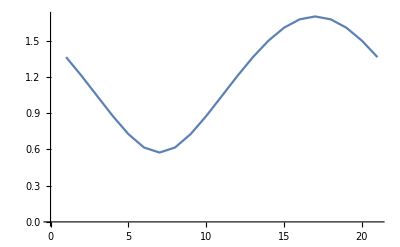

```mathematica
ListLinePlot[RefDis⟦6⟧]
```

```mathematica
Dimensions@𝓉
```

{21}

```mathematica
nbasis[n_Integer,  T_][t_]:=Join[Table[ Cos [ 2 π k t/T ],{k,0,n}],Table[ Sin[ 2 π k t/T ],{k,1,n}]]
```

```mathematica
nbasis[9,2 π][t]
```

{1,Cos[t],Cos[2 t],Cos[3 t],Cos[4 t],Cos[5 t],Cos[6 t],Cos[7 t],Cos[8 t],Cos[9 t],Sin[t],Sin[2 t],Sin[3 t],Sin[4 t],Sin[5 t],Sin[6 t],Sin[7 t],Sin[8 t],Sin[9 t]}

```mathematica
r1 =Fit[Join[{𝓉}ᵀ,{RefDis⟦1⟧}ᵀ,2],nbasis[9,T][t],t];
r2 =Fit[Join[{𝓉}ᵀ,{RefDis⟦2⟧}ᵀ,2],nbasis[9,T][t],t];
r3 =Fit[Join[{𝓉}ᵀ,{RefDis⟦3⟧}ᵀ,2],nbasis[9,T][t],t];
r4 =Fit[Join[{𝓉}ᵀ,{RefDis⟦4⟧}ᵀ,2],nbasis[9,T][t],t];
r5 =Fit[Join[{𝓉}ᵀ,{RefDis⟦5⟧}ᵀ,2],nbasis[9,T][t],t];
r6 =Fit[Join[{𝓉}ᵀ,{RefDis⟦6⟧}ᵀ,2],nbasis[9,T][t],t];
```

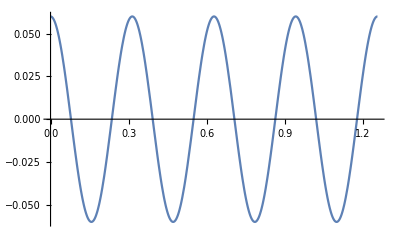

```mathematica
Plot[r1,{t,ti,tf}]
```

```mathematica
ref= {r1,r2,r3,r4,r5,r6};
dref = D[ref, t];
d2ref = D[ref, t,t];
```

```mathematica
𝕥= d2ref + λ (dref-𝕡_♣)+ k 2/π ArcTan[1000 31.82(dref - 𝕡_♣+ λ(ref-𝕢_♣))];
𝕥2 = Dot[Inv@𝕐, Join[Dot[ℂ_♣ᵀ,𝕄_♣,𝕥], -𝕓_♣  ] ];
𝕦★= Dot[Subscript[𝕄, c],𝕥2]; 
SUBS𝕗Control  =Inner[#1 -> #2 &,𝕦,𝕦★ /.SDATA,List];
Eq = Inner[#1 == #2 &,Dot[𝕐,𝕩],𝕪,List];
```

```mathematica
Sola =NDSolve[ Join[((Eq/.SUBS𝕗Control)/.SDATA),CI],Join[𝕢_♣,𝕡_♣],{t,ti,tf},Method->{"EquationSimplification"->"Residual"}];
```

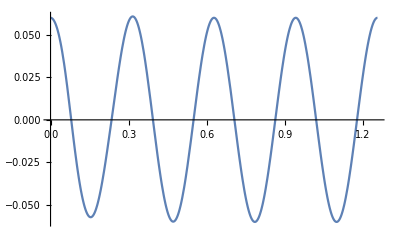

```mathematica
Plot[Subscript[x, p][t]/.Sola, {t,ti,tf}]
```

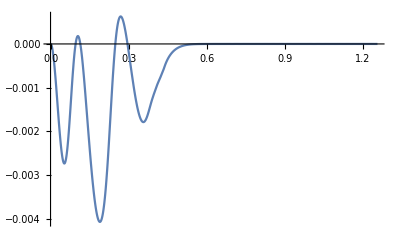

```mathematica
Plot[ref⟦1⟧-Subscript[x, p][t]/.Sola, {t,ti,tf}]
```

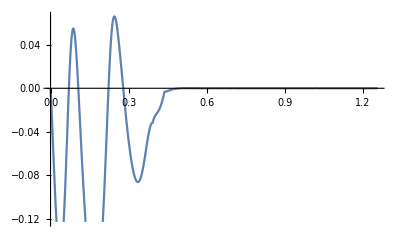

```mathematica
Plot[ (dref⟦1⟧- Subscript[x, p]'[t]) +λ (ref⟦1⟧- Subscript[x, p][t])/.Sola, {t,ti,tf}]
```

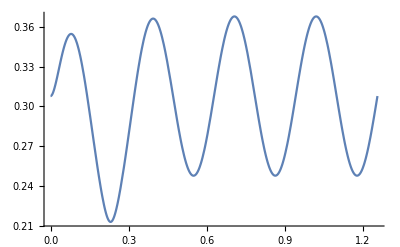

```mathematica
Plot[Subscript[y, p][t]/.Sola, {t,ti,tf}]
```

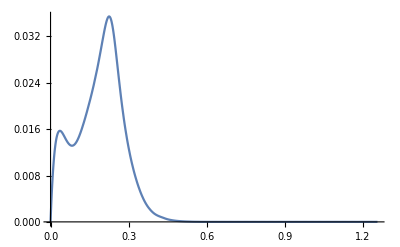

```mathematica
Plot[ref⟦2⟧-Subscript[y, p][t]/.Sola, {t,ti,tf}]
```

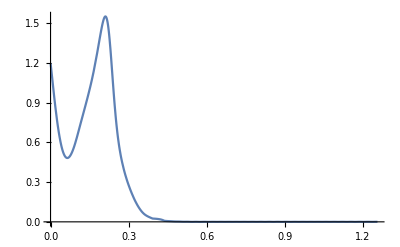

```mathematica
Plot[ (dref⟦2⟧- Subscript[y, p]'[t]) +λ (ref⟦2⟧- Subscript[y, p][t])/.Sola, {t,ti,tf}]
```

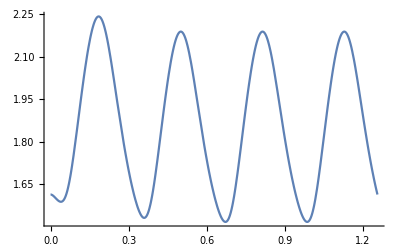

```mathematica
Plot[Subscript[θ, 1,1][t]/.Sola, {t,ti,tf}]
```

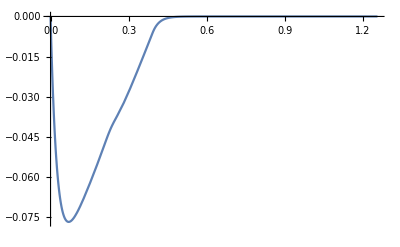

```mathematica
Plot[ref⟦3⟧-Subscript[θ, 1,1][t]/.Sola, {t,ti,tf}]
```

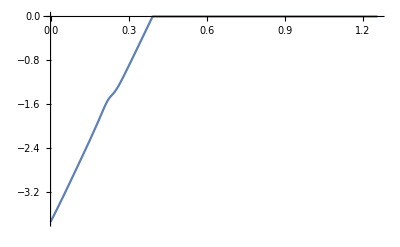

```mathematica
Plot[ (dref⟦3⟧- Subscript[θ, 1,1]'[t]) +λ (ref⟦3⟧- Subscript[θ, 1,1][t])/.Sola, {t,ti,tf}]
```

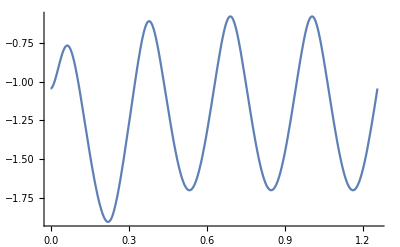

```mathematica
Plot[Subscript[θ, 1,2][t]/.Sola, {t,ti,tf}]
```

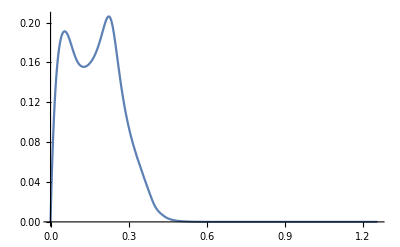

```mathematica
Plot[ref⟦4⟧-Subscript[θ, 1,2][t]/.Sola, {t,ti,tf}]
```

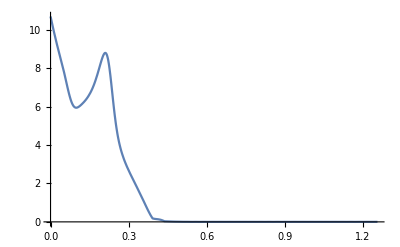

```mathematica
Plot[(dref⟦4⟧- Subscript[θ, 1,2]'[t]) +λ  (ref⟦4⟧- Subscript[θ, 1,2][t])/.Sola, {t,ti,tf}]
```

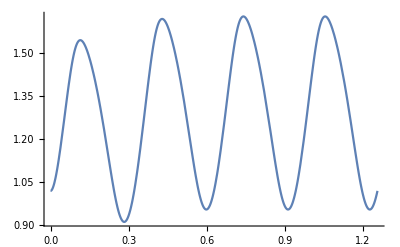

```mathematica
Plot[Subscript[θ, 2,1][t]/.Sola, {t,ti,tf}]
```

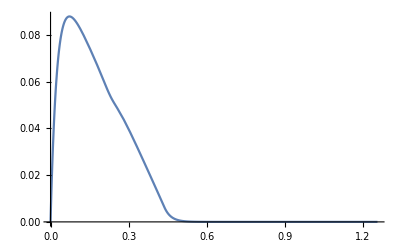

```mathematica
Plot[ref⟦5⟧-Subscript[θ, 2,1][t]/.Sola, {t,ti,tf}]
```

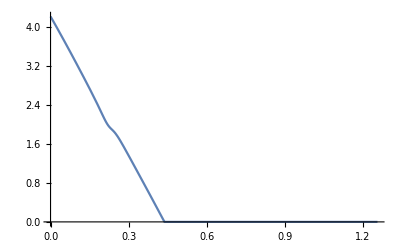

```mathematica
Plot[(dref⟦5⟧- Subscript[θ, 2,1]'[t]) +λ  (ref⟦5⟧- Subscript[θ, 2,1][t])/.Sola, {t,ti,tf}]
```

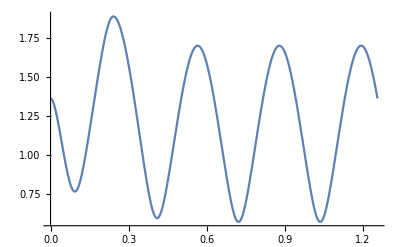

```mathematica
Plot[Subscript[θ, 2,2][t]/.Sola, {t,ti,tf}]
```

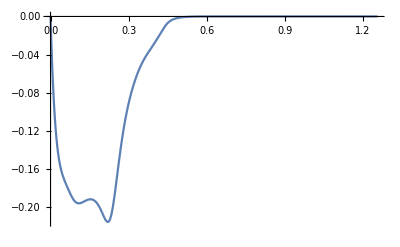

```mathematica
Plot[ref⟦6⟧-Subscript[θ, 2,2][t]/.Sola, {t,ti,tf}]
```

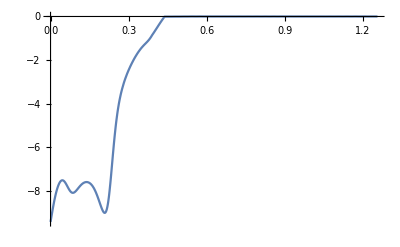

```mathematica
Plot[(dref⟦6⟧- Subscript[θ, 2,2]'[t]) +λ  (ref⟦6⟧- Subscript[θ, 2,2][t])/.Sola, {t,ti,tf}]
```

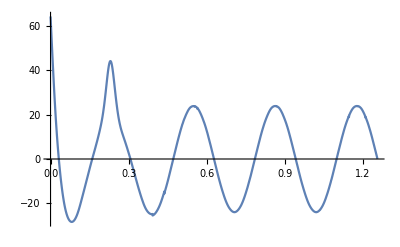

```mathematica
Plot[𝕥2 ⟦2⟧/.SDATA/.Sola, {t,ti,tf}]
```

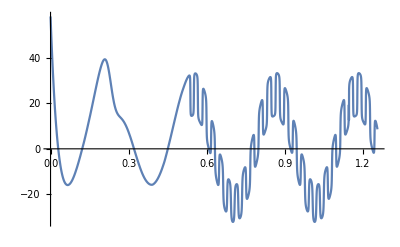

```mathematica
Plot[𝕥⟦2⟧/.SDATA/.Sola, {t,ti,tf}]
```

```mathematica
(*Plot[Dot[{𝕥2 - 𝕥},(𝕥2 - 𝕥)]/.SDATA/.Sola, {t,ti,tf}]*)
```

$Aborted